## 01-starting-out-elementary-arithmetic

```mathematica
1 + 2 + 3
```

6

```mathematica
1 + 2 + 3 + 4 + 5
```

15

```mathematica
1 * 2 * 3 * 4 * 5
```

120

```mathematica
5^2
```

25

```mathematica
3^4
```

81

```mathematica
10^12
```

1000000000000

```mathematica
3^(7*8)
```

523347633027360537213511521

```mathematica
(4-2)*(3+4)
```

14

```mathematica
29000*73
```

2117000

```mathematica
-3 + -2 + -1 + 0 + 1 + 2 + 3
```

```mathematica
-3-2-1+0+1+2+3
```

0

```mathematica
24/3
```

8

```mathematica
5^100
```

7888609052210118054117285652827862296732064351090230047702789306640625

```mathematica
100-(5^2)
```

75

```mathematica
6*(5^2)+7
```

157

```mathematica
(3^2)-(2^3)
```

1

```mathematica
(2^3) * (3^2)
```

72

```mathematica
2*(8 + -11)
```

```mathematica
(8+-11)*2
```

-6

## 02-introducing-functions

```mathematica
Plus[7+6+5]
```

18

```mathematica
Times[2,Plus[3+4]]
```

14

```mathematica
Max[Times[6,8], Times[5,9]]
```

48

```mathematica
RandomInteger[1000]
```

566

```mathematica
Plus[10, RandomInteger[10]]
```

15

```mathematica
Times[5,4,3,2]
```

120

```mathematica
Subtract[2,3]
```

-1

```mathematica
Times[Plus[8,7],Plus[9,2]]
```

165

```mathematica
Divide[Subtract[26,89],9]
```

-7

```mathematica
Subtract[100,Power[5,2]]
```

75

```mathematica
Max[Power[3,5],Power[5,3]]
```

243

```mathematica
Times[3,Max[Power[4,3],Power[3,4]]]
```

243

```mathematica
Plus[RandomInteger[1000], RandomInteger[1000]]
```

1571

## 03-first-look-at-lists

```mathematica
Range[4]
```

{1,2,3,4}

```mathematica
Range[100]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}

```mathematica
Reverse[Range[4]]
```

{4,3,2,1}

```mathematica
Reverse[Range[50]]
```

{50,49,48,47,46,45,44,43,42,41,40,39,38,37,36,35,34,33,32,31,30,29,28,27,26,25,24,23,22,21,20,19,18,17,16,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1}

```mathematica
Join[Range[4], Reverse[Range[4]]]
```

{1,2,3,4,4,3,2,1}

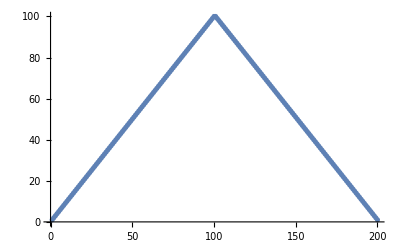

```mathematica
ListPlot[Join[Range[100], Reverse[Range[100]]]]
```

```mathematica
Range[RandomInteger[10]]
```

{1,2,3,4}

```mathematica
Range[10]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
Range[5]
```

{1,2,3,4,5}

```mathematica
Join[Range[10], Range[10],Range[5]]
```

{1,2,3,4,5,6,7,8,9,10,1,2,3,4,5,6,7,8,9,10,1,2,3,4,5}

```mathematica
Join[Range[20], Reverse[Range[20]]]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,20,19,18,17,16,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1}

```mathematica
Range[4]
```

{1,2,3,4}

```mathematica
Join[Range[5], Reverse[Range[4]]]
```

{1,2,3,4,5,4,3,2,1}

```mathematica
Join[Reverse[Range[3]], Reverse[Range[4]], Reverse[Range[5]]]
```

{3,2,1,4,3,2,1,5,4,3,2,1}

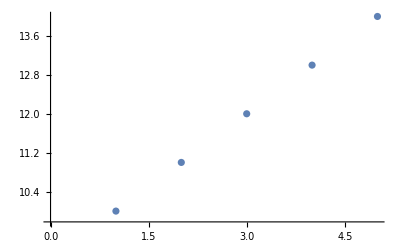

```mathematica
ListPlot[Range[10,14]]
```

```mathematica
Join[Range[10], Reverse[Range[10]], Range[10]]
```

{1,2,3,4,5,6,7,8,9,10,10,9,8,7,6,5,4,3,2,1,1,2,3,4,5,6,7,8,9,10}

## 04-displaying-lists

## BarChart[{1,1,2,3,5}]

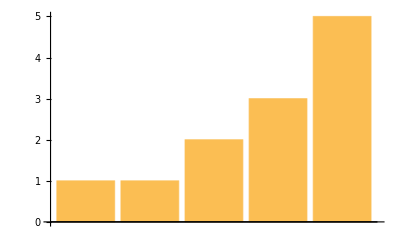

```mathematica
PieChart[Range[10]]
```

-Graphics-

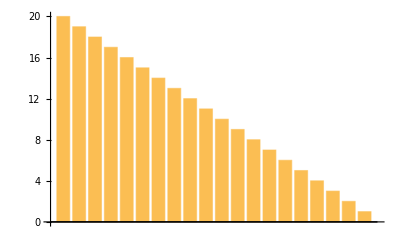

```mathematica
BarChart[Reverse[Range[20]]]
```

```mathematica
Column[Range[5]]
```

1
2
3
4
5

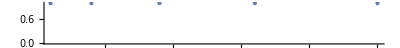

```mathematica
NumberLinePlot[{1,4,9,16,25}]
```

```mathematica
PieChart[{1,1,1,1,1,1,1,1,1,1}]
```

-Graphics-

```mathematica
Column[{PieChart[{1}], PieChart[{1,1}], PieChart[{1,1,1}]}]
```

-Graphics-

```mathematica
List[PieChart[{1}],PieChart[{1,1}],PieChart[{1,1,1}]]
```

{-Graphics-,-Graphics-,-Graphics-}

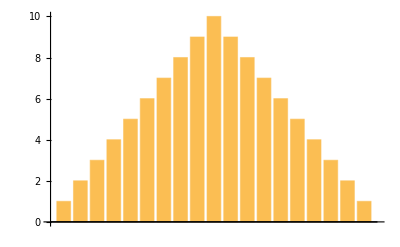

```mathematica
BarChart[Join[Range[10], Reverse[Range[9]]]]
```

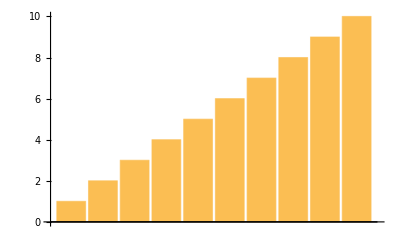
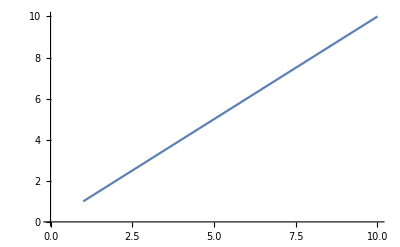
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
{PieChart[Range[10]], BarChart[Range[10]], ListLinePlot[Range[10]]}
```

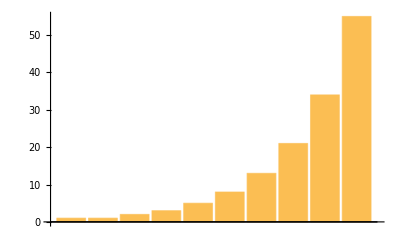
{-Graphics-,-Graphics-}

```mathematica
{PieChart[{1,1,2,3,5,8,13,21,34,55}], BarChart[{1,1,2,3,5,8,13,21,34,55}]}
```

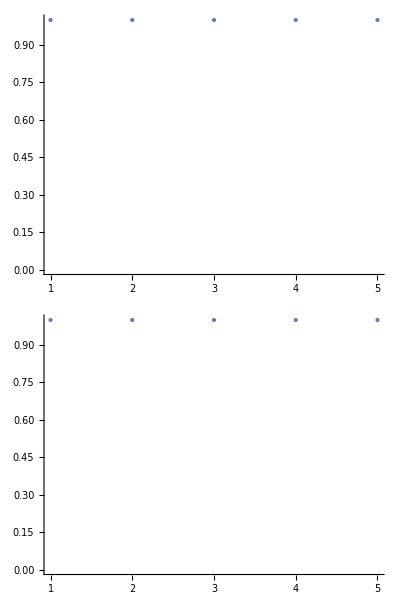

```mathematica
Column[{NumberLinePlot[Range[5]], NumberLinePlot[Range[5]]}]
```

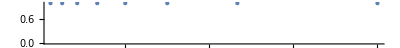

```mathematica
NumberLinePlot[1/Range[2,9]]
```

```mathematica
1/Range[2,9]
```

{1/2,1/3,1/4,1/5,1/6,1/7,1/8,1/9}

## 05-operations-on-lists

```mathematica
Reverse[Range[10]^2]
```

{100,81,64,49,36,25,16,9,4,1}

```mathematica
Total[Range[10]^2]
```

385

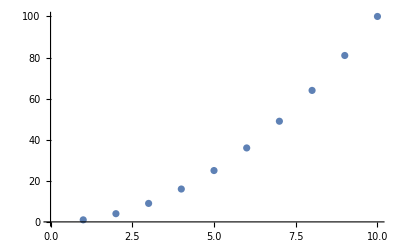

```mathematica
ListPlot[Range[10]^2]
```

```mathematica
Join[Sort[Join[Range[4], Range[4]]]]
```

{1,1,2,2,3,3,4,4}

```mathematica
Range[0,10]+10
```

{10,11,12,13,14,15,16,17,18,19,20}

```mathematica
Sort[Join[Range[5]^2, Range[5]^3]]
```

{1,1,4,8,9,16,25,27,64,125}

```mathematica
Length[IntegerDigits[2^128]]
```

39

```mathematica
First[IntegerDigits[2^32]]
```

4

```mathematica
Take[IntegerDigits[2^100], 10]
```

{1,2,6,7,6,5,0,6,0,0}

```mathematica
Last[Sort[IntegerDigits[2^20]]]
```

8

```mathematica
Count[IntegerDigits[2^1000], 0]
```

28

```mathematica
Part[Sort[IntegerDigits[2^20]],2]
```

1

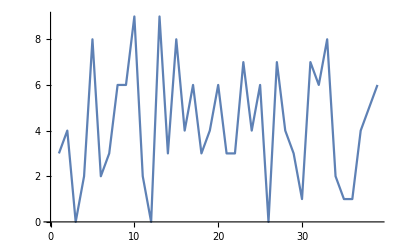

```mathematica
ListLinePlot[IntegerDigits[2^128]]
```

```mathematica
Take[Drop[Range[100],10],10]
```

{11,12,13,14,15,16,17,18,19,20}

```mathematica
3*Range[10]
```

{3,6,9,12,15,18,21,24,27,30}

```mathematica
Times[Range[10], Range[10]]
```

{1,4,9,16,25,36,49,64,81,100}

```mathematica
Last[IntegerDigits[2^37]]
```

2

```mathematica
Last[Take[IntegerDigits[2^32], Length[IntegerDigits[2^32]] - 1]]
```

9

```mathematica
Total[IntegerDigits[3^126]]
```

234

```mathematica
PieChart[IntegerDigits[2^32]]
```

-Graphics-

```mathematica
{PieChart[IntegerDigits[2^20]], PieChart[IntegerDigits[2^40]], PieChart[IntegerDigits[2^60]]}
```

{-Graphics-,-Graphics-,-Graphics-}